## RHS Calculation

```mathematica
l=0.25;
params = {δt-> 0.1, τ-> 1,ϕf->0,ϕa->0,r0->1};
𝔽[θf_]=({{Cos[θf], Sin[θf]*Cos[ϕf]-ⅈ*Sin[θf]*Sin[ϕf]}, {Sin[θf]*Cos[ϕf]+ⅈ*Sin[θf]*Sin[ϕf], -Cos[θf]}});
ℤ=({{1, 0}, {0, -1}});
𝕏[ii_,f_,θa_,θf_]:=1/2(({{1, 0}, {0, 1}})+f*𝔽[θf])
𝕎[ii_,f_,θa_,θf_]:=1/2(({{1, 0}, {0, 1}})+ii*ℤ)
A$wkreal[ii_,f_,θa_,θf_]:=((Cos[θa] (ii+f* Cos[θf])+f* Sin[θa]* Sin[θf] *Cos[ϕa-ϕf])/(1+ii *f*Cos[θf]))/.params

r[ii_,f_,θa_,θf_]:=A$wkreal[ii,f,θa,θf]/Log[2]/.params
P$r[ii_,f_,θa_,θf_]:=l/r0*(δt/(2π*τ))^(1/2)*Exp[-δt/(2*τ)((r[ii,f,θa,θf]/r0)^2+1)]/.params
g$r[ii_,f_,θa_,θf_]:=(r[ii,f,θa,θf]*√l)/(r0^(3/2)*π^(1/4))(δt/(2*τ))^(5/4)*Exp[-δt/(4*τ)((r[ii,f,θa,θf]/r0)^2+1)]/.params

LogHelp[r_]:=If[(x[r]/.params)===Indeterminate,0,x[r]]/.params;
f$wk[ii_,f_,θa_,θf_]:=-Log[2,P$r[ii,f,θa,θf]*Tr[𝕏[ii,f,θa,θf].𝕎[ii,f,θa,θf]]]-(2*Tr[𝕎[ii,f,θa,θf]])/(Log[2]*Sqrt[P$r[ii,f,θa,θf]])*(g$r[ii,f,θa,θf]*A$wkreal[ii,f,θa,θf])/.params
RHS$T1[ii_,f_,θa_,θf_]:=-Log[2,P$r[ii,f,θa,θf]*Tr[𝕏[ii,f,θa,θf].𝕎[ii,f,θa,θf]]]/.params;
h[θa_,θf_]:=Min[f$wk[1,1,θa,θf],f$wk[-1,1,θa,θf],f$wk[1,-1,θa,θf],f$wk[-1,-1,θa,θf]]
RHS$T2[ii_,f_,θa_,θf_]:=-(2*Tr[𝕎[ii,f,θa,θf]])/(Log[2]*Sqrt[l*P$r[ii,f,θa,θf]])*(g$r[ii,f,θa,θf]*A$wkreal[ii,f,θa,θf])/.params
(*ArgMax[{h[θa,θf],0<θa≤π,0<θf≤π}, {θa,θf}]
MaxValue[{h[θa,θf],0<θa≤π,0<θf≤π}, {θa,θf}]*)
```

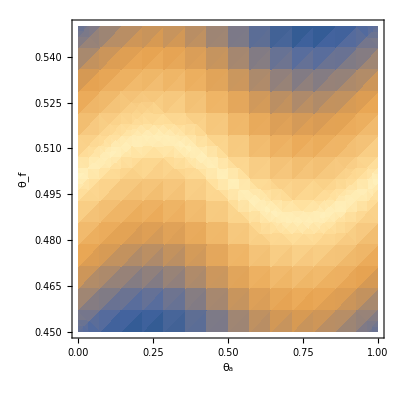

```mathematica
DensityPlot[h[θa*Pi,θf*Pi], {θa,0,1}, {θf,0.45,0.55}, 
LabelStyle-> Large, AxesLabel->{Subscript[θ,"a"],Subscript[θ,f],"RHS"}]
(*Plot3D[RHS$T1[1,-1,θa*Pi,θf*Pi], {θa,0,1}, {θf,0.45,0.55}, 
LabelStyle-> Large, AxesLabel->{Subscript[θ,"a"],Subscript[θ,f],"(RHS^(T1))_(1, -1) "}]*)
(*Plot3D[{RHS$T1[1,-1,θa*Pi,θf*Pi],RHS$T1[1,1,θa*Pi,θf*Pi]}, {θa,0,1}, {θf,0.45,0.55}, 
LabelStyle-> Large, AxesLabel->{Subscript[θ,"a"],Subscript[θ,f],"((RHS^(T1))_both)_ "}]*)
```

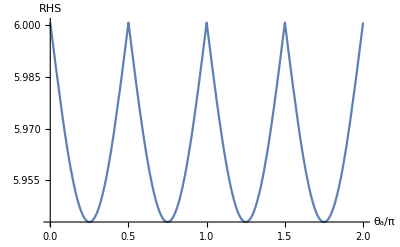

```mathematica
Plot[h[x*Pi,(0.5+0/15) Pi],{x,0,2},AxesLabel->{"θ_a/π","RHS"},LabelStyle->Large]
```

```mathematica
a=0;
mx = MaxValue[ h[x*Pi,(0.5 +a/15)Pi], x]
mn = MinValue[ h[x*Pi,(0.5 +a/15)Pi], x]
(mx-mn)/2
(mx+mn)/2
```

6.00085

5.94285

0.0289989

5.97185

```mathematica
h[0.4 Pi,0.5 Pi]
```

5.96676